{{x→0,y→0}}

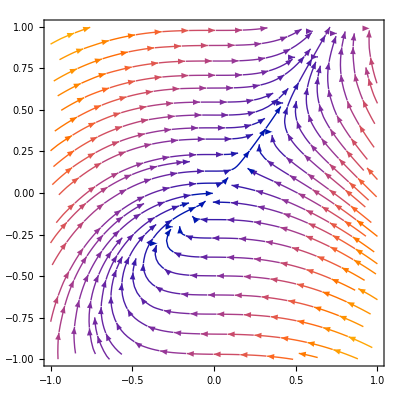

```mathematica
f[x_, y_] := y-x;
g[x_, y_]:=x^2;Solve[f[x,y]==0 && g[x,y]==0, {x,y}]
StreamPlot[{f[x,y], g[x,y]},{x,-1,1},{y,-1,1}]
```

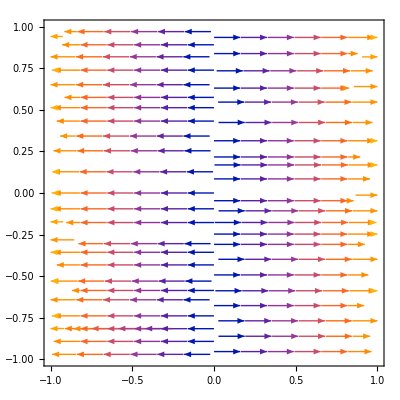

```mathematica
dr[r_] := a*r;
dθ[θ_]:=0;
StreamPlot[{dr[r], 0}/.{a->1},{r,-1,1},{θ,-1,1}]
```

{{x→0,y→0},{x→0,y→0},{x→0,y→0}}

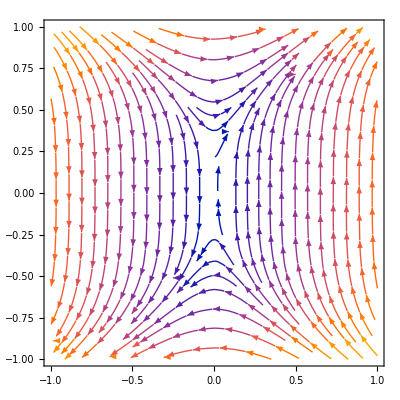

```mathematica
f[x_, y_] := y^3;
g[x_, y_]:=x;Solve[f[x,y]==0 && g[x,y]==0, {x,y}]
StreamPlot[{f[x,y], g[x,y]},{x,-1,1},{y,-1,1}]
```

```mathematica
n = .;
f[x_, y_] := (x^2+y^2)^(Abs[n]/2)*Cos[n*ArcTan[y/x]];
g[x_, y_]:=(x^2+y^2)^(Abs[n]/2)*Sin[n*ArcTan[y/x]];
ϕ[x_,y_] := ArcTan[g[x,y]/f[x,y]];
index = (Integrate[D[ϕ[1,y],y],{y,-1,1}]+Integrate[D[ϕ[x,1],x],{x,1,-1}]+Integrate[D[ϕ[-1,y],y],{y,1,-1}]+Integrate[D[ϕ[x,-1],x],{x,-1,1}])/(2*Pi)
```

n

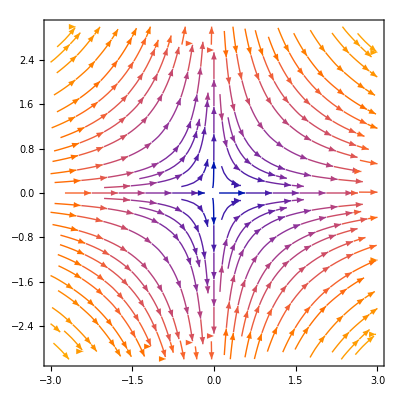

```mathematica
StreamPlot[{f[x,y], g[x,y]}/.n->-1,{x,-3,3},{y,-3,3}]
```